Kaushik Chakram 
                                                                                                                     Professor Julia Kamenetzky
                                                                                                                     phys 425 &01
                                                                                                                     April, 12,2018

```mathematica
$Assumptions = {x,t,m,ω,ℏ,p,a,n} ∈ Reals
```

(x|t|m|ω|ℏ|p|a|n)∈Reals

2)Problem 3.28)

```mathematica
(*We need to define Ψ[x,t] for the infinite square well and define Subscript[E, n].*)
Ene[n_]:=(n^2*π^2*ℏ^2)/(2*m*a^2)
Ψ[n_,x_,t_]:=(√(2/a))*Sin[(n*π*x)/a]*ⅇ^(-((ⅈ*(Ene[n]*t))/ℏ))
```

```mathematica
Φ[n_,p_,t_] = (1/(√(2*π*ℏ)))*Assuming[n≥ 0 && n∈ Integers && a >0 && ℏ >0,Integrate[ⅇ^((-(ⅈ*p*x))/ℏ)*Ψ[n,x,t],{x,0,a}]]
```

(√a ⅇ^(-(ⅈ a p)/ℏ-(ⅈ n^2 π^2 t ℏ)/(2 a^2 m)) ((-1)^(1+n)+ⅇ^((ⅈ a p)/ℏ)) n √π ℏ^(3/2))/((-a p+n π ℏ) (a p+n π ℏ))

```mathematica
(*Let F1[n_,γ_,t_] denote |Subscript[Φ, n][p,t]|^2.
 The limit of function in Mathematica is given by Limit[expr, x-> Subscript[x, 0]] finds the limit of the exprs as x approaches x_0. *)

F1[n_,γ_,t_]:=((2*a*π*n^2)/ℏ)*((1+ (-1)^(n+1)*Cos[γ])/((γ-(n*π))^2*(γ+(n*π))^2))
Limit[F1[2,γ,t],γ->(2*π)] (*Matches the result that we got using Taylor Series expanded till n = 2.*)
```

a/(4 π ℏ)

```mathematica
(*Let's plot this and call the function P1[n,γ,t] to represent|Subscript[Φ, n][p,t]|^2. a will be denoted by j for the command a =j=1 and ℏ=f=1*)
j:=1
f:=1
P1[n_,γ_,t_]:=((2*j*π*n^2)/f)*((1+ (-1)^(n+1)*Cos[γ])/((γ-(n*π))^2*(γ+(n*π))^2))
```

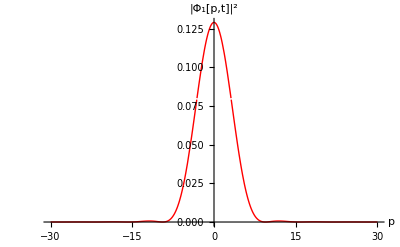

```mathematica
Plot[P1[1,γ,t],{γ,-30,30},PlotRange->Full,PlotStyle->{Red,Thick} ,AxesLabel->{"p"," |Φ_1[p,t]|^2"},LabelStyle->Directive[Bold, Medium]]
```

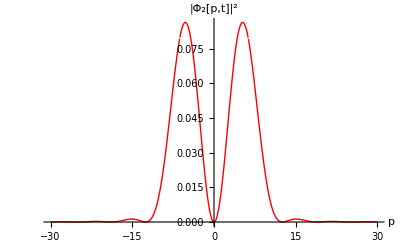

```mathematica
Plot[P1[2,γ,t],{γ,-30,30},PlotRange->Full,PlotStyle->{Red,Thick} ,AxesLabel->{"p"," |Φ_2[p,t]|^2"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
(*Now let's calculate the expectation value of p^2. Where F2[n,p,t] denotes |Subscript[Φ, n][p,t]|^2.*)
F2[n_,p_,t_]:=((2*(n^2*ℏ^3*a*π))/((a^2*p^2-n^2*π^2*ℏ^2)^2))*(1+ (-1)^(n+1)*Cos[(a*p)/ℏ])
Assuming[n≥ 0 && n∈ Integers && a >0 && ℏ >0,Integrate[p^2*F2[n,p,t],{p,-∞,∞}]] (* Stating all assumption so that we get a tidy output.*)
```

(n^2 π^2 ℏ^2)/a^2